```mathematica
N[√2,100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

```mathematica
RealDigits[1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309123`100.]
```

{{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8,0,1,6,8,8,7,2,4,2,0,9,6,9,8,0,7,8,5,6,9,6,7,1,8,7,5,3,7,6,9,4,8,0,7,3,1,7,6,6,7,9,7,3,7,9,9,0,7,3,2,4,7,8,4,6,2,1,0,7,0,3,8,8,5,0,3,8,7,5,3,4,3,2,7,6,4,1,5,7,2},1}

```mathematica
Partition[
{1,4,1,4,2,1,3,5,6,2,3,7,3,0,9,5,0,4,8,8,0,1,6,8,8,7,2,4,2,0,9,6,9,8,0,7,8,5,6,9,6,7,1,8,7,5,3,7,6,9,4,8,0,7,3,1,7,6,6,7,9,7,3,7,9,9,0,7,3,2,4,7,8,4,6,2,1,0,7,0,3,8,8,5,0,3,8,7,5,3,4,3,2,7,6,4,1,5,7,2}
,2,1]
```

{{1,4},{4,1},{1,4},{4,2},{2,1},{1,3},{3,5},{5,6},{6,2},{2,3},{3,7},{7,3},{3,0},{0,9},{9,5},{5,0},{0,4},{4,8},{8,8},{8,0},{0,1},{1,6},{6,8},{8,8},{8,7},{7,2},{2,4},{4,2},{2,0},{0,9},{9,6},{6,9},{9,8},{8,0},{0,7},{7,8},{8,5},{5,6},{6,9},{9,6},{6,7},{7,1},{1,8},{8,7},{7,5},{5,3},{3,7},{7,6},{6,9},{9,4},{4,8},{8,0},{0,7},{7,3},{3,1},{1,7},{7,6},{6,6},{6,7},{7,9},{9,7},{7,3},{3,7},{7,9},{9,9},{9,0},{0,7},{7,3},{3,2},{2,4},{4,7},{7,8},{8,4},{4,6},{6,2},{2,1},{1,0},{0,7},{7,0},{0,3},{3,8},{8,8},{8,5},{5,0},{0,3},{3,8},{8,7},{7,5},{5,3},{3,4},{4,3},{3,2},{2,7},{7,6},{6,4},{4,1},{1,5},{5,7},{7,2}}

```mathematica
Map[First@#->Last@#&,Out[3]]
```

{1→4,4→1,1→4,4→2,2→1,1→3,3→5,5→6,6→2,2→3,3→7,7→3,3→0,0→9,9→5,5→0,0→4,4→8,8→8,8→0,0→1,1→6,6→8,8→8,8→7,7→2,2→4,4→2,2→0,0→9,9→6,6→9,9→8,8→0,0→7,7→8,8→5,5→6,6→9,9→6,6→7,7→1,1→8,8→7,7→5,5→3,3→7,7→6,6→9,9→4,4→8,8→0,0→7,7→3,3→1,1→7,7→6,6→6,6→7,7→9,9→7,7→3,3→7,7→9,9→9,9→0,0→7,7→3,3→2,2→4,4→7,7→8,8→4,4→6,6→2,2→1,1→0,0→7,7→0,0→3,3→8,8→8,8→5,5→0,0→3,3→8,8→7,7→5,5→3,3→4,4→3,3→2,2→7,7→6,6→4,4→1,1→5,5→7,7→2}

```mathematica
Graph[%4]
```

-Graphics-

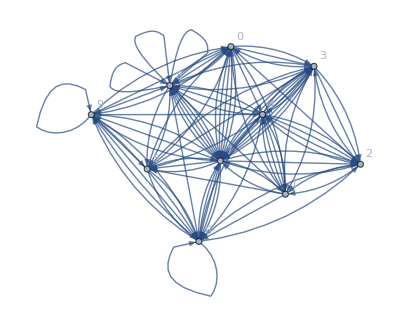

```mathematica
Show[SetProperty[%5,VertexLabels->"Name"],PlotRange->All]
```

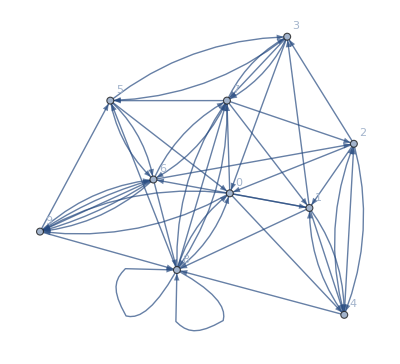

```mathematica
Graph[Map[First@#->Last@#&,Partition[First@RealDigits@N[√2,50],2,1]],VertexLabels->"Name"]
```

```mathematica
Manipulate[
Graph[
Map[
First@#->Last@#&,
Partition[
First@
RealDigits@
N[√2,n],
2,1]
],VertexLabels->"Name"]
,{n,1,1000,1}]
```

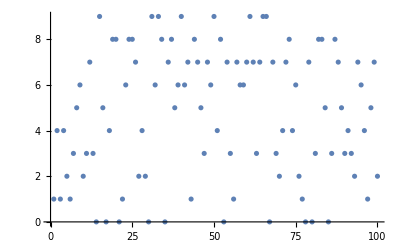

```mathematica
ListPlot[
First@
RealDigits@
N[√2,100]]
```

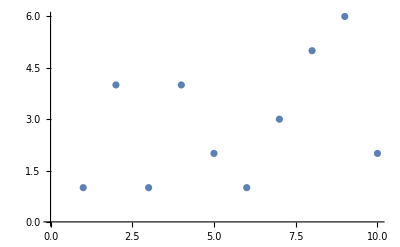
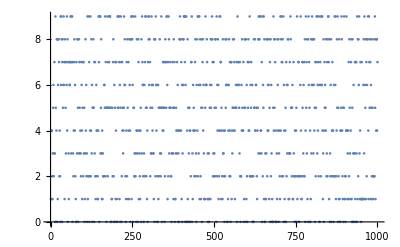
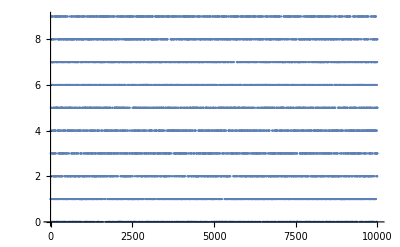
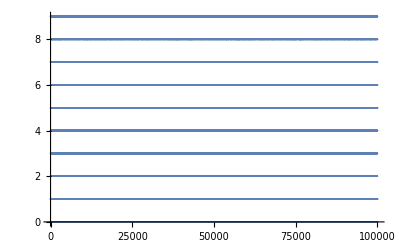
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
ListPlot[
First@
RealDigits@
N[√2,10^i]],{i,1,5}]
```

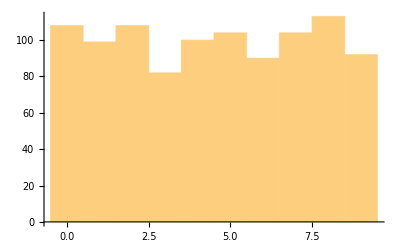

```mathematica
Histogram@First@
RealDigits@
N[√2,1000]
```

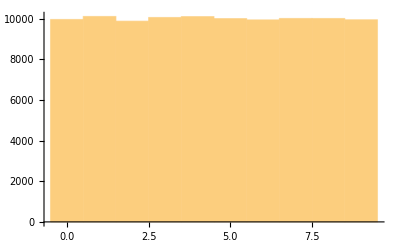

```mathematica
Histogram@
First@
RealDigits@
N[√2,100000]
```

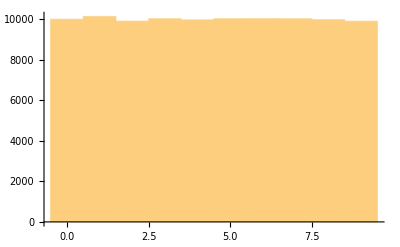

```mathematica
Histogram@
First@
RealDigits@
N[π,100000]
```

```mathematica
Table[
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,10}]
```

{0,Log[2],-(2 Log[2])/3+Log[3],-Log[2]+Log[4],-(4 Log[2])/5+Log[5],1/6 (-2 Log[2]-3 Log[3])+Log[6],1/7 (-2 Log[2]-3 Log[3])+Log[7],1/8 (-2 Log[2]-3 Log[3])+Log[8],1/9 (-2 Log[2]-3 Log[3])+Log[9],1/10 (-4 Log[2]-3 Log[3])+Log[10]}

```mathematica
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,10}]
```

{0.,0.693147,0.636514,0.693147,1.05492,1.0114,1.27703,1.49418,1.67699,1.69574}

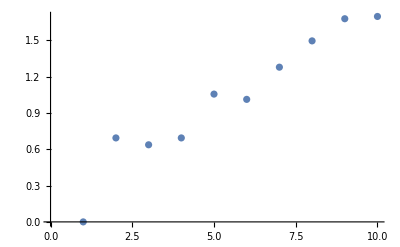

```mathematica
ListPlot[{0.,0.6931471805599453,0.636514168294813,0.6931471805599453,1.0549201679861442,1.0114042647073518,1.277034259466139,1.4941751382893083,1.6769877743224173,1.6957425341696348}]
```

```mathematica
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,1000}]
```

{0.,0.693147,0.636514,0.693147,1.05492,1.0114,1.27703,1.49418,1.67699,1.69574,1.72019,1.86368,1.84462,1.80951,2.08377,2.10068,2.11928,2.11002,2.20516,2.2241,2.2187,2.20052,2.22341,2.22441,2.21341,2.23798,2.24278,2.23642,2.23173,2.22009,2.25441,2.26335,2.27269,2.26495,2.25849,2.26964,2.25949,2.27147,2.2748,2.2786,2.27667,2.28142,2.28063,2.27202,2.2725,2.27893,2.28555,2.28288,2.27733,2.28313,2.28581,2.27892,2.27851,2.27537,2.27939,2.27999,2.27543,2.2738,2.27009,2.26469,2.2669,2.26047,2.26319,2.25926,2.25982,2.25522,2.25628,2.24913,2.25068,2.25766,2.26181,2.25462,2.25311,2.25545,2.25433,2.25915,2.26184,2.26279,2.25644,2.25619,2.25764,2.25633,2.25398,2.26194,2.26105,2.26161,2.25881,2.25357,2.25948,2.2593,2.26185,2.2608,2.26505,2.26008,2.26047,2.26213,2.26516,2.26969,2.26481,2.26802,2.26287,2.26204,2.26547,2.2657,2.26802,2.26675,2.26559,2.26708,2.26771,2.27033,2.26882,2.27056,2.27164,2.27347,2.27535,2.27363,2.27838,2.27474,2.27453,2.27509,2.2782,2.27787,2.27791,2.27868,2.27823,2.27728,2.27823,2.27798,2.28137,2.28392,2.28326,2.28512,2.28457,2.28188,2.28098,2.2781,2.27836,2.28049,2.28032,2.28127,2.28225,2.28273,2.28437,2.28396,2.28509,2.28682,2.287,2.28456,2.28532,2.2852,2.28471,2.28694,2.28653,2.28851,2.28858,2.28791,2.28895,2.28914,2.28978,2.28894,2.28885,2.28844,2.28773,2.28899,2.28984,2.29032,2.29211,2.29126,2.28962,2.29104,2.2913,2.29234,2.29302,2.29336,2.2925,2.2909,2.29134,2.29149,2.29199,2.29219,2.29211,2.2896,2.2896,2.28993,2.2897,2.28978,2.29084,2.29159,2.2912,2.2906,2.28913,2.28998,2.28924,2.28927,2.2905,2.29032,2.28993,2.2885,2.28921,2.29023,2.28872,2.28846,2.28898,2.28926,2.28861,2.28824,2.28939,2.28886,2.28729,2.2859,2.28634,2.28759,2.28719,2.28819,2.28627,2.28489,2.2844,2.28413,2.28269,2.28381,2.28324,2.2839,2.28482,2.28599,2.28383,2.28503,2.28625,2.28723,2.28699,2.2866,2.28718,2.28798,2.28674,2.28643,2.28751,2.28692,2.28739,2.28613,2.28684,2.28716,2.2881,2.28904,2.28959,2.2893,2.29007,2.28997,2.29058,2.29035,2.29062,2.29108,2.29193,2.29208,2.29132,2.29091,2.29037,2.29028,2.2912,2.29194,2.29066,2.29034,2.29113,2.29084,2.29147,2.29195,2.29243,2.2931,2.29275,2.29312,2.29233,2.29272,2.29312,2.29369,2.29343,2.29372,2.29402,2.29368,2.29336,2.2937,2.29391,2.29403,2.29332,2.29431,2.29407,2.29491,2.29458,2.295,2.29572,2.29543,2.29575,2.29537,2.29433,2.2941,2.29377,2.29345,2.29384,2.29424,2.29395,2.29437,2.29304,2.2927,2.29315,2.29387,2.29422,2.29355,2.29326,2.29299,2.2935,2.29389,2.29356,2.29421,2.2939,2.29433,2.29488,2.29521,2.29544,2.29589,2.29625,2.2961,2.29636,2.29652,2.2967,2.29602,2.29654,2.29695,2.29678,2.2972,2.29696,2.29673,2.29708,2.29753,2.29733,2.29706,2.2968,2.29698,2.29728,2.29696,2.29666,2.29707,2.29667,2.29632,2.29614,2.29573,2.29618,2.29587,2.29624,2.2958,2.29545,2.29496,2.29477,2.29451,2.29475,2.29437,2.29393,2.29437,2.29417,2.29311,2.29357,2.29413,2.29368,2.29399,2.29322,2.29345,2.29378,2.29331,2.29279,2.29234,2.29178,2.29155,2.29125,2.29117,2.29148,2.2917,2.29126,2.2907,2.29088,2.29146,2.29172,2.29114,2.29069,2.29061,2.29114,2.29159,2.29174,2.29116,2.29171,2.2918,2.29136,2.29184,2.2924,2.29233,2.29239,2.29282,2.2927,2.29299,2.29244,2.29331,2.29355,2.29371,2.29403,2.29362,2.29408,2.29463,2.29451,2.29459,2.29473,2.29522,2.29519,2.29504,2.29485,2.29507,2.29469,2.29457,2.29415,2.29399,2.29466,2.29451,2.29432,2.29466,2.29476,2.29524,2.29487,2.29466,2.29478,2.29452,2.29413,2.29445,2.29471,2.29443,2.29447,2.29416,2.29426,2.29366,2.29337,2.29349,2.29397,2.29446,2.29471,2.29435,2.29455,2.2946,2.29475,2.29442,2.29458,2.29459,2.29471,2.29445,2.29492,2.29505,2.29472,2.29508,2.29517,2.29493,2.29504,2.29473,2.2953,2.2958,2.29592,2.29631,2.2963,2.29675,2.29648,2.29657,2.29635,2.29606,2.29581,2.29587,2.29604,2.29641,2.29653,2.29697,2.29735,2.29769,2.29802,2.29727,2.29761,2.29791,2.29816,2.29822,2.298,2.29831,2.29843,2.29826,2.29853,2.29862,2.29843,2.29866,2.2984,2.29864,2.29884,2.29891,2.29863,2.29884,2.29876,2.2988,2.2988,2.29862,2.29872,2.29882,2.29861,2.29868,2.29875,2.29848,2.29852,2.29852,2.29849,2.29821,2.29843,2.29802,2.29804,2.29827,2.29855,2.2985,2.2987,2.29894,2.29895,2.29868,2.29914,2.29887,2.29926,2.29911,2.29892,2.29915,2.29891,2.2991,2.2991,2.2993,2.29928,2.2994,2.2995,2.29967,2.29966,2.29958,2.29972,2.29969,2.29966,2.29944,2.29967,2.29962,2.29982,2.29974,2.2999,2.2998,2.30001,2.30015,2.30029,2.30023,2.30021,2.30032,2.30021,2.30016,2.30006,2.29992,2.29977,2.29997,2.30008,2.30022,2.30004,2.29999,2.29979,2.29988,2.29981,2.29965,2.29971,2.29991,2.29971,2.29948,2.29965,2.29941,2.29925,2.29917,2.29899,2.29938,2.29951,2.29934,2.29914,2.29924,2.299,2.29917,2.29896,2.29898,2.29892,2.29891,2.29888,2.29897,2.29907,2.29905,2.29881,2.29889,2.29893,2.29873,2.29867,2.29891,2.29867,2.29865,2.29839,2.29835,2.29827,2.29821,2.29843,2.29854,2.29853,2.29845,2.29827,2.29802,2.29794,2.29801,2.29782,2.29755,2.29799,2.29798,2.29795,2.29806,2.29781,2.29762,2.29757,2.2975,2.2976,2.29753,2.29745,2.29737,2.29727,2.29721,2.29698,2.29672,2.29666,2.29672,2.29676,2.29685,2.29692,2.29666,2.29659,2.29686,2.29689,2.29662,2.29656,2.29657,2.297,2.29692,2.29707,2.29697,2.29699,2.29736,2.29738,2.29739,2.29763,2.2975,2.29777,2.29755,2.2975,2.29759,2.29766,2.29745,2.29773,2.29764,2.29758,2.2975,2.29774,2.298,2.29824,2.29845,2.29836,2.29825,2.29821,2.29823,2.29833,2.29834,2.29842,2.2983,2.29853,2.29832,2.29823,2.29816,2.29804,2.298,2.29807,2.29829,2.29822,2.29844,2.29835,2.29824,2.2983,2.29817,2.29819,2.29807,2.29786,2.29773,2.29765,2.29754,2.29756,2.29743,2.29729,2.29752,2.29775,2.29761,2.2977,2.29771,2.29756,2.29742,2.29763,2.29763,2.29763,2.29761,2.298,2.29798,2.29811,2.29797,2.29792,2.29791,2.29784,2.29769,2.2979,2.29779,2.29766,2.29777,2.29775,2.29797,2.29783,2.29781,2.29766,2.29751,2.29745,2.29743,2.29753,2.29776,2.29785,2.29771,2.29756,2.29777,2.29799,2.29819,2.29839,2.29833,2.29831,2.29865,2.2985,2.29836,2.29821,2.29821,2.29805,2.29814,2.29833,2.2985,2.29845,2.29862,2.29861,2.29858,2.29847,2.29848,2.29836,2.29832,2.29831,2.29816,2.29833,2.29818,2.29836,2.29831,2.29825,2.29821,2.29815,2.29802,2.29787,2.2978,2.29772,2.29766,2.29798,2.29799,2.29816,2.29832,2.29823,2.29818,2.29805,2.29798,2.29818,2.29829,2.2982,2.29812,2.29802,2.29794,2.29781,2.29768,2.29797,2.29785,2.29777,2.29797,2.29788,2.29804,2.29791,2.29806,2.29796,2.29808,2.298,2.29788,2.29774,2.29776,2.29762,2.29778,2.29768,2.29788,2.2978,2.29813,2.29803,2.29812,2.29801,2.29819,2.29828,2.29815,2.29818,2.29807,2.29793,2.29787,2.29781,2.2977,2.29757,2.29743,2.29791,2.29809,2.29817,2.2982,2.29812,2.29829,2.29819,2.29806,2.29814,2.298,2.29792,2.29799,2.29817,2.29803,2.29814,2.29806,2.29829,2.29832,2.2985,2.29869,2.2986,2.29847,2.29849,2.29842,2.29833,2.29839,2.29829,2.29831,2.29821,2.29816,2.29835,2.29827,2.29821,2.29831,2.29818,2.29829,2.29821,2.29841,2.2983,2.29819,2.29837,2.29831,2.29837,2.29826,2.29814,2.29808,2.2981,2.29803,2.29804,2.29804,2.29797,2.29785,2.29791,2.29809,2.29793,2.29784,2.29776,2.29797,2.29817,2.29808,2.29808,2.29799,2.29803,2.29801,2.29789,2.29783,2.29773,2.29793,2.29783,2.29801,2.2979,2.29777,2.29778,2.29777,2.29784,2.29779,2.29769,2.29768,2.29758,2.29776,2.2977,2.29757,2.29764,2.29757,2.29774,2.2979,2.2978,2.29768,2.29757,2.29749,2.29763,2.29761,2.29759,2.29774,2.29796,2.29792,2.29806,2.29804,2.29794,2.29786,2.2978,2.29801,2.29815,2.29811,2.29808,2.298,2.29812,2.29801,2.29795,2.29786,2.29774,2.29796,2.29806,2.29794,2.29814,2.29832,2.2983,2.29842,2.29829,2.29826,2.29822,2.2984,2.29851,2.29836,2.29847,2.2984,2.29832,2.29823,2.29819,2.29843,2.2986,2.29871,2.29869,2.29866,2.29876,2.29863,2.29872,2.29868,2.29876,2.29883,2.29889,2.29894,2.29905,2.29897,2.29896,2.29923,2.29927,2.29938,2.29935,2.29926,2.2993,2.29926,2.2992,2.2993,2.29922,2.2993,2.29921,2.29921,2.29915,2.29932,2.29928,2.29925,2.29916,2.29911,2.29914,2.29924,2.29921,2.29911,2.29906,2.29908,2.29904,2.29899,2.299,2.29894,2.29884,2.29877,2.29896,2.29878,2.29874,2.29875,2.29865,2.29866,2.29855,2.29844,2.29845,2.29841}

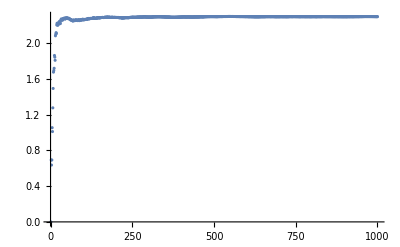

```mathematica
ListPlot[%19]
```

```mathematica
ListPlot@
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,1000}]
```

-Graphics-

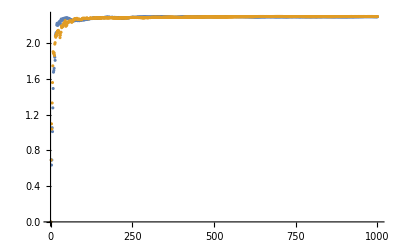

```mathematica
ListPlot[{
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,1000}]
,Table[
N@
Entropy@
First@
RealDigits@
N[π,i]
,{i,1,1000}]
}]
```

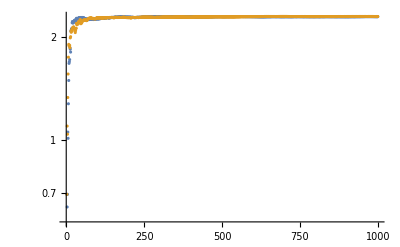

```mathematica
ListLogPlot[{
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,1000}]
,Table[
N@
Entropy@
First@
RealDigits@
N[π,i]
,{i,1,1000}]
}]
```

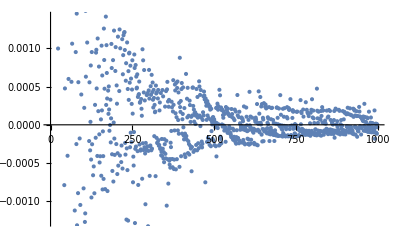

```mathematica
ListPlot@
Differences@
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,1000}]
```

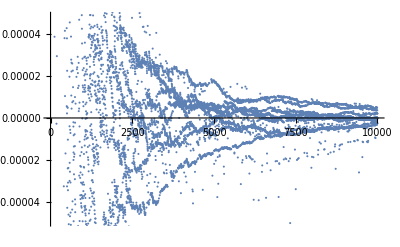

```mathematica
ListPlot@
Differences@
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,10000}]
```

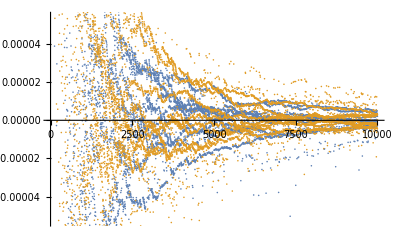

```mathematica
ListPlot[{
Differences@
Table[
N@
Entropy@
First@
RealDigits@
N[√2,i]
,{i,1,10000}],
Differences@
Table[
N@
Entropy@
First@
RealDigits@
N[π,i]
,{i,1,10000}]
}]
```

```mathematica
Manipulate[
Graph[
Map[
First@#->Last@#&,
Partition[
First@
RealDigits@
N[√2,n],
2,1]
],VertexLabels->"Name"]
,{n,1,1000,1}]
```

```mathematica
n(n-1)
```

(-1+n) n

```mathematica
Collect[(-1+n) n,n]
```

-n+n^2

```mathematica
n^2
```

n^2

```mathematica
FourierSequenceTransform[n^2,n,ω]
```

FourierSequenceTransform[n^2,n,ω]

```mathematica
RandomInteger[{0,1}]
```

1

```mathematica
RandomInteger[{0,1},10]
```

{0,1,1,1,0,1,1,1,0,0}

```mathematica
randomBool[n_]:=Map[If[#==0,False,True]&,RandomInteger[{0,1},n]]
```

```mathematica
randomBool[10]
```

{False,True,True,False,False,False,True,False,False,False}

```mathematica
Not/@{False,True,True,False,False,False,True,False,False,False}
```

{True,False,False,True,True,True,False,True,True,True}

```mathematica
{
{False,True,True,False,False,False,True,False,False,False},
{True,False,False,True,True,True,False,True,True,True}
}
```

{{False,True,True,False,False,False,True,False,False,False},{True,False,False,True,True,True,False,True,True,True}}

```mathematica
randomBool[3]
```

{True,False,False}

```mathematica
Not/@{True,False,False}
```

{False,True,True}

```mathematica
{{True,False,False},{False,True,True}}
```

{{True,False,False},{False,True,True}}

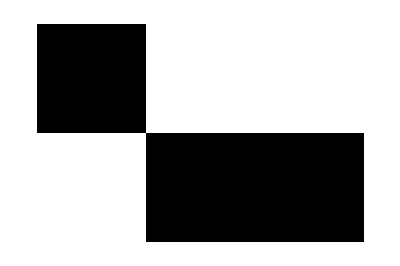

```mathematica
ArrayPlot[Boole[{{True,False,False},{False,True,True}}]]
```

```mathematica
{{True,False,False},{False,True,True},{False,False,False}}
```

{{True,False,False},{False,True,True},{False,False,False}}

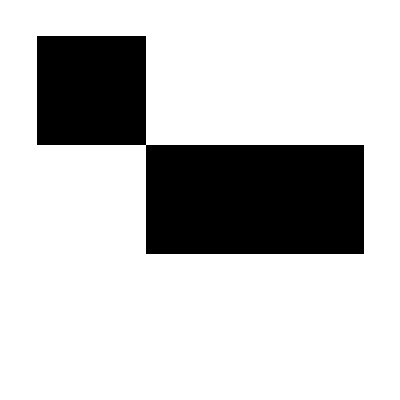

```mathematica
ArrayPlot[Boole[{{True,False,False},{False,True,True},{False,False,False}}]]
```

```mathematica
{{True,False,False},{False,True,True},{False,False,False}}
```

```mathematica
Transpose@{{True,False,False},{False,True,True}}
```

{{True,False},{False,True},{False,True}}

```mathematica
Xor/@Transpose@{{True,False,False},{False,True,True}}
```

{{True,False},{False,True},{False,True}}

```mathematica
Apply[Xor,#]&/@Transpose@{{True,False,False},{False,True,True}}
```

{True,True,True}

```mathematica
Apply[Xor,#]&/@Transpose@{{True,False,False},{False,True,True}}
```

```mathematica
Apply[Xor,#]&/@Transpose@{{True,False,False},{False,True,True},{True,True,True}}
```

{False,False,False}

```mathematica
{{True,False,False},{False,True,True},{True,True,True}}
```

{{True,False,False},{False,True,True},{True,True,True}}

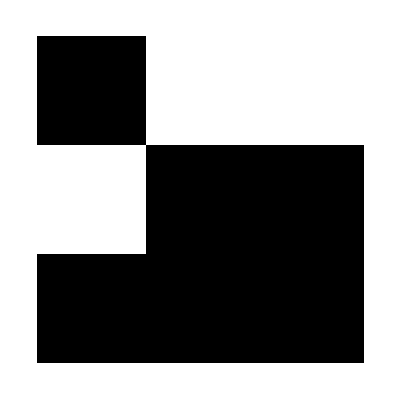

```mathematica
ArrayPlot[Boole[{{True,False,False},{False,True,True},{True,True,True}}]]
```

```mathematica
{{True,False,False},{False,True,True},{True,True,True},{False,False,False}}
```

{{True,False,False},{False,True,True},{True,True,True},{False,False,False}}

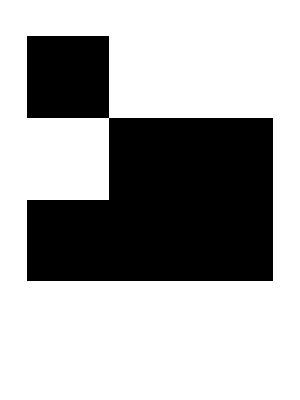

```mathematica
ArrayPlot[Boole[{{True,False,False},{False,True,True},{True,True,True},{False,False,False}}]]
```

```mathematica
{True}
```

{True}

```mathematica
{{True},{False}}
```

{{True},{False}}